```mathematica
smat=IdentityMatrix[40];
smat[[2,2]]=r;
For[i=1,i<39,i++,smat[[i+2,i+2]]=r smat[[i,i]]];
hmat=IdentityMatrix[40];
For[i=1,i≤40,i++,hmat[[i,i]]=0];
For[i=1,i<40,i=i+2,hmat[[i,i+1]]=t1+γ/2;hmat[[i+1,i]]=t1-γ/2];
For[i=2,i<40,i=i+2,hmat[[i,i+1]]=t2;hmat[[i+1,i]]=t2];
Inverse[smat].hmat.smat//TraditionalForm
```

(0 | r (t1+γ/2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(t1-γ/2)/r | 0 | t2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | t2 | 0 | r (t1+γ/2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | (t1-γ/2)/r | 0 | t2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | t2 | 0 | r (t1+γ/2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | (t1-γ/2)/r | 0 | t2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | t2 | 0 | r (t1+γ/2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | (t1-γ/2)/r | 0 | t2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | t2 | 0 | r (t1+γ/2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (t1-γ/2)/r | 0 | t2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | t2 | 0 | r (t1+γ/2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (t1-γ/2)/r | 0 | t2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | t2 | 0 | r (t1+γ/2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (t1-γ/2)/r | 0 | t2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | t2 | 0 | r (t1+γ/2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (t1-γ/2)/r | 0 | t2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | t2 | 0 | r (t1+γ/2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (t1-γ/2)/r | 0 | t2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | t2 | 0 | r (t1+γ/2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (t1-γ/2)/r | 0 | t2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | t2 | 0 | r (t1+γ/2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (t1-γ/2)/r | 0 | t2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | t2 | 0 | r (t1+γ/2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (t1-γ/2)/r | 0 | t2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | t2 | 0 | r (t1+γ/2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (t1-γ/2)/r | 0 | t2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | t2 | 0 | r (t1+γ/2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (t1-γ/2)/r | 0 | t2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | t2 | 0 | r (t1+γ/2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (t1-γ/2)/r | 0 | t2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | t2 | 0 | r (t1+γ/2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (t1-γ/2)/r | 0 | t2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | t2 | 0 | r (t1+γ/2) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (t1-γ/2)/r | 0 | t2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | t2 | 0 | r (t1+γ/2) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (t1-γ/2)/r | 0 | t2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | t2 | 0 | r (t1+γ/2) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (t1-γ/2)/r | 0 | t2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | t2 | 0 | r (t1+γ/2)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (t1-γ/2)/r | 0)

```mathematica
Manipulate[Plot[{√((1+t2 Cos[k])^2+(t2 Sin[k])^2),-√((1+t2 Cos[k])^2+(t2 Sin[k])^2)},{k,-Pi,Pi}],{t2,-2,2}]
```

```mathematica
result=Simplify[Solve[((t1-γ/2)+t2 β)((t1+γ/2)+t2 β^-1)==e,β]]
```

{{β→(4 e-4 t1^2-4 t2^2+γ^2-√(16 t2^2 (-4 t1^2+γ^2)+(4 e-4 t1^2-4 t2^2+γ^2)^2))/(4 t2 (2 t1+γ))},{β→(4 e-4 t1^2-4 t2^2+γ^2+√(16 t2^2 (-4 t1^2+γ^2)+(4 e-4 t1^2-4 t2^2+γ^2)^2))/(4 t2 (2 t1+γ))}}

```mathematica
e=0;
Simplify[result[[1,1,2]]]
```

-(4 t1^2+4 t2^2-γ^2+√((-4 t1^2+4 t2^2+γ^2)^2))/(8 t1 t2+4 t2 γ)

```mathematica
t2=1;
g=4/3;
t1=1.2;
Clear[t1];
r=√Abs[(t1-g/2)/(t1+g/2)];
a1=Table[ParametricPlot[{{t1-g/2+t2 r Cos[t],t2 r Sin[t]},{t1+g/2+t2/r Cos[t],t2/r Sin[t]}},{t,-Pi,Pi},PlotRange->{{-4,4},{-3,3}},PlotLegends->{"d_-","d_+"},AxesLabel->{"Re","Im"},Frame->True,GridLines->Automatic,FrameLabel->{Subscript[d, x],Subscript[d, y]},PlotLabel->{"t1",t1}],{t1,-3,3,0.02}];
Export["Chern.gif",a1]
```

Chern.gif

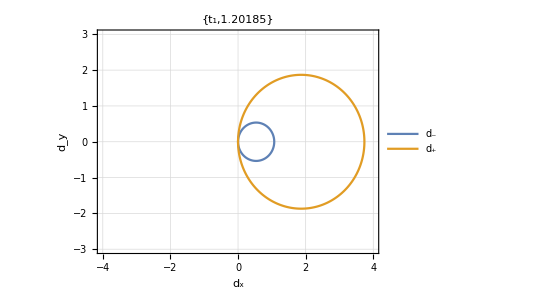

```mathematica
t2=1;
g=4/3;
t1=N[√((t2)^2+g^2/4)];
r=√Abs[(t1-g/2)/(t1+g/2)];
a2=ParametricPlot[{{t1-g/2+t2 r Cos[t],t2 r Sin[t]},{t1+g/2+t2/r Cos[t],t2/r Sin[t]}},{t,-Pi,Pi},PlotRange->{{-4,4},{-3,3}},PlotLegends->{"d_-","d_+"},AxesLabel->{"Re","Im"},Frame->True,GridLines->Automatic,FrameLabel->{Subscript[d, x],Subscript[d, y]},PlotLabel->{"t_1" ,t1}]
```

```mathematica
For[i=1,i≤300,i++,Export["dcomplex",a[i]]]
```

C:\Users\Fluen\Desktop\李成蹊所有的note\non-hermitian\dcomplex\dcomplex.png

```mathematica
6/0.02
```

300.

```mathematica
MapIndexed[Export[ToString@First@#2<>".png",#]&,a1]
SystemOpen@Directory[]
```

{1.png,2.png,3.png,4.png,5.png,6.png,7.png,8.png,9.png,10.png,11.png,12.png,13.png,14.png,15.png,16.png,17.png,18.png,19.png,20.png,21.png,22.png,23.png,24.png,25.png,26.png,27.png,28.png,29.png,30.png,31.png,32.png,33.png,34.png,35.png,36.png,37.png,38.png,39.png,40.png,41.png,42.png,43.png,44.png,45.png,46.png,47.png,48.png,49.png,50.png,51.png,52.png,53.png,54.png,55.png,56.png,57.png,58.png,59.png,60.png,61.png,62.png,63.png,64.png,65.png,66.png,67.png,68.png,69.png,70.png,71.png,72.png,73.png,74.png,75.png,76.png,77.png,78.png,79.png,80.png,81.png,82.png,83.png,84.png,85.png,86.png,87.png,88.png,89.png,90.png,91.png,92.png,93.png,94.png,95.png,96.png,97.png,98.png,99.png,100.png,101.png,102.png,103.png,104.png,105.png,106.png,107.png,108.png,109.png,110.png,111.png,112.png,113.png,114.png,115.png,116.png,117.png,118.png,119.png,120.png,121.png,122.png,123.png,124.png,125.png,126.png,127.png,128.png,129.png,130.png,131.png,132.png,133.png,134.png,135.png,136.png,137.png,138.png,139.png,140.png,141.png,142.png,143.png,144.png,145.png,146.png,147.png,148.png,149.png,150.png,151.png,152.png,153.png,154.png,155.png,156.png,157.png,158.png,159.png,160.png,161.png,162.png,163.png,164.png,165.png,166.png,167.png,168.png,169.png,170.png,171.png,172.png,173.png,174.png,175.png,176.png,177.png,178.png,179.png,180.png,181.png,182.png,183.png,184.png,185.png,186.png,187.png,188.png,189.png,190.png,191.png,192.png,193.png,194.png,195.png,196.png,197.png,198.png,199.png,200.png,201.png,202.png,203.png,204.png,205.png,206.png,207.png,208.png,209.png,210.png,211.png,212.png,213.png,214.png,215.png,216.png,217.png,218.png,219.png,220.png,221.png,222.png,223.png,224.png,225.png,226.png,227.png,228.png,229.png,230.png,231.png,232.png,233.png,234.png,235.png,236.png,237.png,238.png,239.png,240.png,241.png,242.png,243.png,244.png,245.png,246.png,247.png,248.png,249.png,250.png,251.png,252.png,253.png,254.png,255.png,256.png,257.png,258.png,259.png,260.png,261.png,262.png,263.png,264.png,265.png,266.png,267.png,268.png,269.png,270.png,271.png,272.png,273.png,274.png,275.png,276.png,277.png,278.png,279.png,280.png,281.png,282.png,283.png,284.png,285.png,286.png,287.png,288.png,289.png,290.png,291.png,292.png,293.png,294.png,295.png,296.png,297.png,298.png,299.png,300.png,301.png}

```mathematica
p1=Plot[y=0,{x,-3,-1.2},PlotRange->{{-3,3},{-0.5,1.5}},Frame->True,PlotStyle->Directive[Red,Thick],FrameLabel->{"t_1","W"}];
p2=Plot[y=1,{x,-1.2,1.2},PlotRange->{{-3,3},{-0.5,1.5}},Frame->True,PlotStyle->Directive[Red,Dashed,Thick]];
p3=Plot[y=0,{x,1.2,3},PlotRange->{{-3,3},{-0.5,1.5}},Frame->True,PlotStyle->Directive[Red,Thick]];
p=Show[p1,p2,p3];
Export["windingnumber.pdf",p]
```

windingnumber.pdf